```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/oernst/Research/cnl/dynamic_boltzmann_cpp

Params

```mathematica
nOpt=1000;
```

```mathematica
numin=-1.0;
numax=1.5;
nnu=41;
dnu=(numax-numin)/(nnu-1);
nuGrid=Table[numin+i*dnu,{i,0,nnu-1}];
```

```mathematica
nuInit=1.04;
```

```mathematica
boxLength=3;
```

In depth

```mathematica
Manipulate[
f=Import["data/F/"<>IntegerString[iOptStep,10,4]<>".txt","Table"];
nu=Import["data/nu_traj/"<>IntegerString[iOptStep,10,4]<>".txt","Table"];
var=Import["data/var_traj/"<>IntegerString[iOptStep,10,4]<>".txt","Table"];
moments=Import["data/moments/"<>IntegerString[iOptStep,10,4]<>".txt","Table"];
tvals=nu[[;;,1]];
nuTraj=nu[[;;,2]];
varSel=var[[inuVal;;,3]][[;;;;nnu]];
momentsFromnu=Table[(27 ⅇ^x)/(1+ⅇ^x),{x,nuTraj}];
pltave=ListLinePlot[{moments[[;;,2]],moments[[;;,3]],momentsFromnu}];
pltvar=ListLinePlot[{varSel,varSel*Table[Exp[-(nuTraj[[it]]-nuGrid[[inuVal]])^2/(2*0.1)],{it,1,Length[nu]}]},PlotLabel->nuGrid[[inuVal]]];
pltf=Show[{
ListLinePlot[f,PlotStyle->Black,PlotRange->All],
Plot[-1-ⅇ^x,{x,numin,numax}],
ListLinePlot[{{nuGrid[[inuVal]],-6},{nuGrid[[inuVal]],0}},PlotStyle->Gray]
},PlotRange->All];
pltnu=Show[
Plot[-Log[-1+ⅇ^t (1+ⅇ^-nuInit)],{t,0,1}]
,
ListLinePlot[nu,PlotStyle->Black]
];

GraphicsGrid[{{pltf,pltnu},{pltave,pltvar}}]
,{iOptStep,0,nOpt-1,1},{{inuVal,25},1,Length[nuGrid],1}]
```

```mathematica
cum={};
AppendTo[cum,(moments[[1,2]]-moments[[1,3]])*interp[tvals[[1]],nuVal]];
Do[
AppendTo[cum,cum[[-1]]+(moments[[t,2]]-moments[[t,3]])*interp[tvals[[t]],nuVal]];
,{t,2,Length[tvals]}]
```

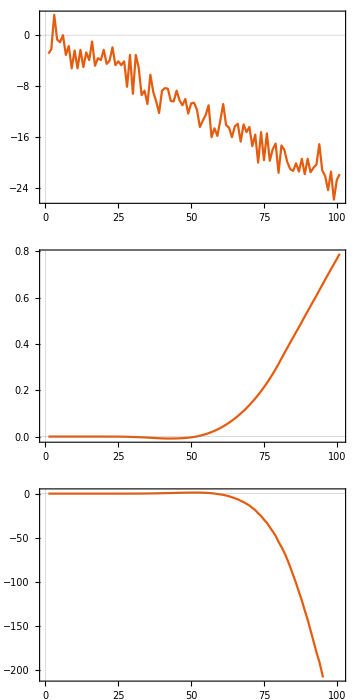

```mathematica
GraphicsColumn[{
ListLinePlot[moments[[;;,2]]-moments[[;;,3]]],
ListLinePlot[Table[interp[tvals[[t]],nuVal],{t,1,Length[tvals]}]],
ListLinePlot[cum]
},ImageSize->Medium]
```

Moments

```mathematica
Manipulate[
moments=Import["data/moments/"<>IntegerString[i,10,4]<>".txt","Table"];
GraphicsColumn[{
Show[
ListLinePlot[moments[[;;,{1,2}]],PlotRange->All,PlotStyle->Black]
,
ListLinePlot[moments[[;;,{1,3}]],PlotRange->All,PlotStyle->Black]
]
}]
,
{i,0,nOpt-1,1}]
```

Variational term

```mathematica
Manipulate[
nu=Import["data/nu_traj/"<>IntegerString[i,10,4]<>".txt","Table"];
var=Import["data/var_traj/"<>IntegerString[i,10,4]<>".txt","Table"];
GraphicsColumn[{
Show[
ListContourPlot[var]
,
ListLinePlot[nu,PlotRange->All,PlotStyle->Black]
]
}]
,
{i,0,nOpt-1,1}]
```

Basis function

```mathematica
z=Sum[Binomial[boxLength^3,n]*Exp[n*v[t]],{n,0,Infinity}]
```

1+27 ⅇ^v[t]+351 ⅇ^(2 v[t])+2925 ⅇ^(3 v[t])+17550 ⅇ^(4 v[t])+80730 ⅇ^(5 v[t])+296010 ⅇ^(6 v[t])+888030 ⅇ^(7 v[t])+2220075 ⅇ^(8 v[t])+4686825 ⅇ^(9 v[t])+8436285 ⅇ^(10 v[t])+13037895 ⅇ^(11 v[t])+17383860 ⅇ^(12 v[t])+20058300 ⅇ^(13 v[t])+20058300 ⅇ^(14 v[t])+17383860 ⅇ^(15 v[t])+13037895 ⅇ^(16 v[t])+8436285 ⅇ^(17 v[t])+4686825 ⅇ^(18 v[t])+2220075 ⅇ^(19 v[t])+888030 ⅇ^(20 v[t])+296010 ⅇ^(21 v[t])+80730 ⅇ^(22 v[t])+17550 ⅇ^(23 v[t])+2925 ⅇ^(24 v[t])+351 ⅇ^(25 v[t])+27 ⅇ^(26 v[t])+ⅇ^(27 v[t])

```mathematica
ave=Sum[n*Binomial[boxLength^3,n]*Exp[n*v[t]]/z,{n,0,Infinity}]
```

(27 ⅇ^v[t])/(1+ⅇ^v[t])

```mathematica
Solve[(ave==ave0)/.v[t]->v,v]
```

{{v→ConditionalExpression[2 ⅈ π C[1]+Log[-ave0/(-27+ave0)],C[1]∈Integers]}}

```mathematica
Log[-20/(-27+20)]//N
```

1.04982

```mathematica
Log[-10/(-27+10)]//N
```

-0.530628

```mathematica
Solve[(D[ave,t]==-ave)/.v'[t]->dv,dv]
```

{{dv→-1-ⅇ^v[t]}}

```mathematica
DSolve[
-1-ⅇ^v[t]==v'[t]&&v[0]==v0,v[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{v[t]→-Log[-1+ⅇ^t (1+ⅇ^-v0)]}}

```mathematica
Manipulate[
f=Import["data/F/"<>IntegerString[i,10,4]<>".txt","Table"];
Show[{
ListLinePlot[f,PlotRange->All,PlotStyle->Black]
,
Plot[Exp[x]-1,{x,-3,-1}]
},PlotRange->All]
,
{i,0,nOpt-1,1}]
```